# Inlämningsuppgift 1: Problemlösning

IX1307 Problemlösning i Matematik, Inlämningsuppgift 1a, HT2017

Notebook mall och problem 3.2 och 3.3 av Göran Andersson

## 1. Inledning

Denna uppgift går ut på att lösa ett antal matematiska problem med hjälp av Mathematica och skriva en kort rapport direkt i en egen Notebook. Rapporten skall, för varje uppgift, beskriva: problemet, figur, ange namn på variabler, lösningen till problemet inklusive resonemang och sedan diskutera resultatet.

Plagiering är inte tillåten, och källor måste anges när ni referera till annat material. Lämna in både en pdf-fil och notebook-filen i Canvas. Pdf-filen behövs för plagiatkontroll, då *.nb inte är accepeterad i URKUND.

## 2. Nyttiga funktioner i Mathematica

Här är en kort beskrivning av några funktioner som kan vara nyttiga att känna till för att lösa problemen nedan. För mer informatino om funktionerna se Wolfram Documentation under hjälp-menyn.

#### Komplexa tal

Den imaginära enheten representeras av ett versalt I i Mathematica.

```mathematica
I*I
```

-1

Roten av ett negativt tal :

```mathematica
Sqrt[-4]
```

2 ⅈ

Algebra med komplexa tal fungera som vanligt:

```mathematica
(4+3 I)/(2-I)
```

1+2 ⅈ

```mathematica
z1=Exp[2+9 I]
```

ⅇ^(2+9 ⅈ)

Funktionen N kan användas för att beräkna numeriska närmevärde av exempelvis z_1

```mathematica
N[z1]
```

-6.73239+3.04517 ⅈ

eller av andra tal. Här är Pi med 50 siffrors noggranhet:

```mathematica
N[Pi, 50]
```

3.1415926535897932384626433832795028841971693993751

Olika funktioner kan sedan användas för att manipulera komplexa tal:

```mathematica
z2=4+3I;
```

Realdel:

```mathematica
Re[z2]
```

4

Imaginärdel

```mathematica
Im[z2]
```

3

Komplexa konjugatet till z_2

```mathematica
Conjugate[z2]
```

4-3 ⅈ

och till z_1

```mathematica
Conjugate[z1]
```

ⅇ^(2-9 ⅈ)

Absolutbeloppet till z_2

```mathematica
Abs[z2]
```

5

Argumentet till z_1

```mathematica
Arg[z2]
```

ArcTan[3/4]

För att grafiskt representera komplexa talplanet används ListPlot. Vi börjar med att skapa en lista av talen:

```mathematica
cn={z1, Conjugate[z1], z2, Conjugate[z2]}
```

{ⅇ^(2+9 ⅈ),ⅇ^(2-9 ⅈ),4+3 ⅈ,4-3 ⅈ}

Sedan kan listan av tal konverteras till en list av talpar {realdel, imaginärdel}

```mathematica
pp=Table[{Re[cn[[i]]], Im[cn[[i]]]}, {i, 1, 4}]
```

{{ⅇ^2 Cos[9],ⅇ^2 Sin[9]},{ⅇ^2 Cos[9],Im[ⅇ^(2-9 ⅈ)]},{4,3},{4,-3}}

Här är en de komplexa talen ritade i det komplexa talplanet:

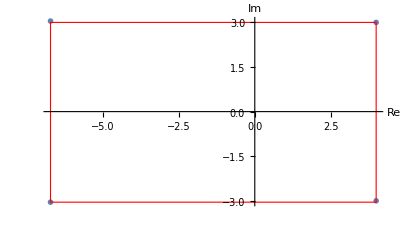

```mathematica
ListPlot[pp, AxesLabel->{"Re", "Im"}, AspectRatio->Automatic,PlotMarkers->{Automatic, Medium},Epilog->{ EdgeForm[Red],FaceForm[],Rectangle[{pp[[3,1]], pp[[3,2]]}, {pp[[2, 1]], pp[[2, 2]]}], }]
```

#### Summor

Sum används för att beräkna en summa. Om det finns ett utryck för varje element av summan kan skriva den direkt

```mathematica
Sum[n^2, {n, 1, 10}]
```

385

För att bestämma de 10:e primtalet kan man använda

```mathematica
Prime[10]
```

29

Funktionen Sum kan då användas för att summera de 100 första primtalen.

```mathematica
Sum[Prime[i], {i, 1, 100}]
```

24133

## 3. Problem

Lös nedanstående problem. Problemets lösning och resultat skall innehålla visualisering där det är relevant.

### Polynomekvation

Hitta lösningarna till polynomekvationen: x^5-2 x^4-19/4 x^3+31/4 x^2+11/2 x-15/2=0.

### Ekvation med absolutbelopp

Lös ekvationen |x-1|+|x+2|=3.

### Binomisk ekvation

Finn lösningen till ekvationen z^7=1-i och visa grafiskt att dessa ligger på en cirkel i komplexa talplanet.

### Akilles och sköldpaddan

Akilles och sköldpaddan är en av Zenons paradoxer. Antag att Akilles springer 10 gånger så fort som sköldpaddan. De båda skall tävla vem som först kommer i mål på 100 meter. Då sköldpaddan är långsammare än Akilles så får den ett försprång på 80 meter. Paradoxen är att när Akilles har sprungit dessa 80 meter, så har sköldpaddan kommit 8 meter, när Akilles har sprungit dessa 8 meter har sköldpaddan kommit 8 dm. Det resonemanget skulle leda till att Akilles aldrig i kapp sköldpaddan. Undersök och förklara paradoxen, samt ta fram en lösning när Akilles kommer i kapp sköldpaddan.